```mathematica
Clear[A]
```

# Classical Mechanics

```mathematica
$Assumptions=q1∈Reals&&q2∈Reals&&q3∈Reals&&p1∈Reals&&p2∈Reals&&p3&&H∈Reals;
```

## Angular Momentum is Conserved

```mathematica
q={q1[t],q2[t],q3[t]};
p={p1[t],p2[t],p3[t]};
H=(p.p)/(2m)+U[√(q.q)];
```

Define Angular Momentum

```mathematica
L={Lx[t],Ly[t],Lz[t]}=Cross[q,p];
```

Define Poisson Bracket

```mathematica
PB[A_,B_]:=Sum[D[A,q[[i]]]D[B,p[[i]]]-D[B,q[[i]]]D[A,p[[i]]],{i,1,3}]
PBDecomp[A_,B_]:=Table[D[A,q[[i]]]D[B,p[[i]]]-D[B,q[[i]]]D[A,p[[i]]],{i,1,3}]
```

Determine if angular momentum is conserved, AKA find the Poisson Bracket with Hamiltonian

```mathematica
PB[L,H];
PBDecomp[L[[1]],H][[2]];
D[L[[1]],q[[3]]]D[H,p[[3]]]
```

-(p2[t] p3[t])/m

```mathematica
L[[1]]
```

p3[t] q2[t]-p2[t] q3[t]

```mathematica
Dt[L,t]==D[L,t]
```

True

## Show L generates rotations

We want to show that the coordinate transform for associated with generating function L is a rotation of coordinates. 
For L_z, the generating function is:
L_z= p_x y-p_y x

```mathematica
dL=L[[3]];
PB[dL,q]
PB[dL,p]
```

{q2[t],-q1[t],0}

{p2[t],-p1[t],0}

Note that these transformations align with the following rotation of x,y,z
δ x=y ⅆθ
δ y=-xⅆθ
δ z= 0
These changes also correspond to changing the momentum:
δ p_x=p_y ⅆθ
δ p_y=-p_xⅆθ
δ p_z= 0
This requires the Generating function G to have the following partials:
∂_p_x G=y
∂_p_y G=-x
∂_x G=p_y
∂_y G=-p_x
Notice that L_z matches these conditions:

```mathematica
{D[L[[3]],p[[1]]],D[L[[3]],p[[2]]],D[L[[3]],q[[1]]],D[L[[3]],q[[2]]]}/.{p1[t]->"p_x",p2[t]->"p_y",p3[t]->"p_z",q1[t]->"x",q2[t]->"y",q3[t]->"z"}
```

{-y,x,p_y,-p_x}

```mathematica
TransformedHamiltonian=(FullSimplify[H/.{q1[t]->q1[t]-q2[t]ⅆθ,q2[t]->q2[t]+q1[t]ⅆθ,q3[t]->q3[t],p1[t]->p1[t]-p2[t]ⅆθ,p2[t]->p2[t]+p1[t]ⅆθ,p3[t]->p3[t]}//Simplify])
```

1/(2 m)((1+(ⅆθ)^2) p1[t]^2+(1+(ⅆθ)^2) p2[t]^2+p3[t]^2+2 m U[√((1+(ⅆθ)^2) (q1[t]^2+q2[t]^2)+q3[t]^2)])

## Show A is also Conserved

Define new Hamiltonian with explicit potential and additional Quantity A

```mathematica
H1=H/.{U[√(q.q)]->-k/(√(q.q))};
A=Cross[p,L]-m k q/(√(q.q));
```

Calculate PB:

```mathematica
PB[H1,A]//Simplify
(PBDecomp[H1,A[[1]]]//Total)/.{1/((q1[t]^2+q2[t]^2+q3[t]^2)^(3/2))->1/r^3,1/(√(q1[t]^2+q2[t]^2+q3[t]^2))->1/r,p1[t]->"p_1",p2[t]->"p_2",p3[t]->"p_3",q1[t]->"q_1",q2[t]->"q_2",q3[t]->"q_3"}//Expand
```

{0,0,0}

-(p_1 q_1^2 k)/r^3-(p_1 q_2^2 k)/r^3-(p_1 q_3^2 k)/r^3+(p_1 k)/r

Check if total derivative is same as partial

```mathematica
FullSimplify[Dt[A,t]==D[A,t],Assumptions->{Dt[k,t]==0,Dt[m,t]==0}]
```

True

## Relate A to the total energy

A.A=(p × L-m k r̂).(p × L-m k r̂)=
=m^2 k^2+(p × L).(p × L)-2m k r̂.(p × L)
Using the following vector identity:
A.(B×C)=B.(C×A)=C.(A×B)
We can rewrite the last one as:
r̂.(p × L)=L.(r̂×p)=1/r L.(r×p)=L^2/r  
So the dot of A with itself is:
A.A =m^2 k^2+(p × L).(p × L)-(2m k L^2)/r
         = m^2 k^2+2m(1/(2m)(p × L).(p × L)-(k L^2)/r)
Using another vector identity:
(A × B).(A × B)=A^2 B^2-(A.B)^2
Since L is defined as a cross product of p, their dot product is zero, and hence we just get:
A.A=m^2 k^2+2m((p^2 L^2)/(2m)-(k L^2)/r)
        =m^2 k^2+2m L^2 E
A^2 = m^2 k^2+2m L^2 E
Meaning:

```mathematica
((A.A-m^2 k^2)/(2m L[t].L[t])==H1)//Simplify
```

True

The Expression for an orbit, which is a conic section of eccentricity ϵ is:
1/r=C(1+ ϵ cosθ)
We can find this by taking a dot product of A with the position vector r:
A r cosθ =A.r= r.(p×L)-m k r
Using reasoning from above, the triple product can be rewritten:
r.(p×L)=(r×p).L=L.L=L^2
Meaning:
L^2=m k r +A r cosθ
L^2/r=m k + A cosθ
1/r=(m k)/L^2(1+A/(m k)cosθ)
We can then identify:
C=(m k)/L^2
ϵ=A/(m k)
We can then replace the A in our expression for the energy with the eccentricity:
A^2=m^2 k^2 ϵ^2
m^2 k^2 ϵ^2=m^2 k^2+2m L^2 E
ϵ^2=1+(2 L^2)/(m k^2)E

## Extension to Quantum Problem

Check conserved quantities:

```mathematica
0==PB[H1,L.L]//Simplify
0==PB[H1,L[[3]]]//Simplify
0==PB[H1,H1]//Simplify
0==PB[H1,A.A]//Simplify
```

True

True

True

«1 more identical outputs»

Initial attempts to solve the Hydrogen atom involved analyzing it in terms of the symmetry group SO(4), meaning we should have to use 4 orthogonal symmetry directions in order to describe it fully, we already know the following conservation laws:

Energy Conservation (H)

Total Angular Momentum Conservation

# Electrodynamics

```mathematica
ClearAll["Global`*"]
```

## E and P everywhere

```mathematica
dispField=Solve[q==Integrate[d r^2 Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}],d][[1,1]]
eField=Solve[e==d/(Subscript[ϵ, 0](1+χ))/.dispField,e][[1,1]]
pField=Solve[p==Subscript[ϵ, 0] χ e/.eField,p][[1,1]]
```

d→q/(4 π r^2)

e→q/(4 π r^2 (1+χ) ϵ_0)

p→(q χ)/(4 π r^2 (1+χ))

## Bound Charge Densities

## Total Bound Charge on Surface

## Net Charge, Why?

# Quantum Mechanics

```mathematica
ψp=1/(√2)(Subscript[ψ, a][Subscript[r, 1]]Subscript[ψ, b][Subscript[r, 2]]+Subscript[ψ, b][Subscript[r, 1]]Subscript[ψ, a][Subscript[r, 2]]);
ψm=1/(√2)(Subscript[ψ, a][Subscript[r, 1]]Subscript[ψ, b][Subscript[r, 2]]-Subscript[ψ, b][Subscript[r, 1]]Subscript[ψ, a][Subscript[r, 2]]);
FullSimplify[Conjugate[ψm]ψm,Assumptions->Subscript[ψ, a][r]∈Complexes]//Expand
```

-1/2 Conjugate[-ψ_a[r_2] ψ_b[r_1]+ψ_a[r_1] ψ_b[r_2]] ψ_a[r_2] ψ_b[r_1]+1/2 Conjugate[-ψ_a[r_2] ψ_b[r_1]+ψ_a[r_1] ψ_b[r_2]] ψ_a[r_1] ψ_b[r_2]

```mathematica
Conjugate[(1+I)(1+2I)]==(Conjugate[1+I])(Conjugate[1+2I])//Reduce
```

True

```mathematica
E0+A+B-(E0+A-B)
```

2 B

```mathematica
sds[j_,j1_,j2_]:=j(j+1)-j1(j1+1)-j2(j2+1);
sds[0,1/2,1/2]
```

-3/2

```mathematica
(E0+(ℏ^2 κ)/4)-(E0-(3 ℏ^2 κ)/4)
```

κ ℏ^2

# Statistical Mechanics

Fermi Wavevector

```mathematica
nplus = Integrate[1/(2π)^3 k^2 Sin[θ],{k,0,kFp},{θ,0,π},{ϕ,0,2π}];
nminus= Integrate[1/(2π)^3 k^2 Sin[θ],{k,0,kFm},{θ,0,π},{ϕ,0,2π}];
kp=Solve[np==nplus/.kFp^3->kFp,kFp][[1,1]]
km=Solve[nm==nminus/.kFm^3->kFm,kFm][[1,1]]
```

kFp→6 np π^2

kFm→6 nm π^2

Kinetic Energy

```mathematica
(kFp/.kp)^(5/3)+(kFm/.km)^(5/3)//Factor
```

6 6^(2/3) (nm^(5/3)+np^(5/3)) π^(10/3)

```mathematica
6^(5/3)
```

6 6^(2/3)

```mathematica
ℏ^2/(20 m π^2)(6 π^2)^(5/3)
```

(3 3^(2/3) π^(4/3) ℏ^2)/(5 2^(1/3) m)

```mathematica
Integrate[ℏ^2/((2π)^3 2m)k^2 k^2 Sin[θ],{k,0,kFp},{θ,0,π},{ϕ,0,2π}]
```

(kFp^5 ℏ^2)/(20 m π^2)

Deviations

```mathematica
Clear[n]
```

```mathematica
pdev=Series[(1+δ)^(5/3),{δ,0,4}]//Normal
mdev=Series[(1-δ)^(5/3),{δ,0,4}]//Normal
pdev+mdev
pdev=Series[(n/2+δ)^(5/3),{δ,0,4}]//Normal
mdev=Series[(n/2-δ)^(5/3),{δ,0,4}]//Normal
pdev+mdev
```

1+(5 δ)/3+(5 δ^2)/9-(5 δ^3)/81+(5 δ^4)/243

1-(5 δ)/3+(5 δ^2)/9+(5 δ^3)/81+(5 δ^4)/243

2+(10 δ^2)/9+(10 δ^4)/243

n^(5/3)/(2 2^(2/3))+(5 n^(2/3) δ)/(3 2^(2/3))+(5 2^(1/3) δ^2)/(9 n^(1/3))-(10 2^(1/3) δ^3)/(81 n^(4/3))+(20 2^(1/3) δ^4)/(243 n^(7/3))

n^(5/3)/(2 2^(2/3))-(5 n^(2/3) δ)/(3 2^(2/3))+(5 2^(1/3) δ^2)/(9 n^(1/3))+(10 2^(1/3) δ^3)/(81 n^(4/3))+(20 2^(1/3) δ^4)/(243 n^(7/3))

n^(5/3)/2^(2/3)+(10 2^(1/3) δ^2)/(9 n^(1/3))+(40 2^(1/3) δ^4)/(243 n^(7/3))

```mathematica
ℏ^2/(20m π^2)(6 π^2)^(5/3)(n/2)^(5/3)40/(9 n^2)
```

(2 π^(4/3) ℏ^2)/(3^(1/3) m n^(1/3))

```mathematica
(6)^(5/3)(1/2)^(5/3)
```

3 3^(2/3)

```mathematica
4*10/9
```

40/9

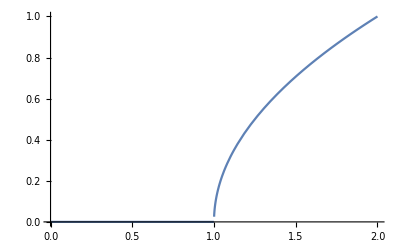

```mathematica
Plot[UnitStep[x-1] √(x-1),{x,0,2}]
```

```mathematica
40/(9 n^2)((ℏ^2(6 π^2)^(5/3))/(20 m π^2)(n/2)^(5/3))
```

(2 π^(4/3) ℏ^2)/(3^(1/3) m n^(1/3))

```mathematica
(n/2+δ)(n/2-δ)//Expand
```

n^2/4-δ^2

```mathematica
((ℏ^2(6 π^2)^(5/3))/(20 m π^2 n^(1/3)))(10/9)2^(1/3)
```

(2 π^(4/3) ℏ^2)/(3^(1/3) m n^(1/3))

```mathematica
(2 (1/n)^(1/3) π^(4/3) ℏ^2)/(3^(1/3) m)-(2 π^(4/3) ℏ^2)/(3^(1/3) m n^(1/3))//Simplify
```

(2 (-1+(1/n)^(1/3) n^(1/3)) π^(4/3) ℏ^2)/(3^(1/3) m n^(1/3))